### Notations

```mathematica
Off[Part::partw]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CreateSymbolEn.wl"]
```

```mathematica
Unprotect[E1,E2,E3,X1,Id,N11,N12,N13,α1,v1,v1c,α1l,α1h];
ClearAll[E1,E2,E3,X1,Id,N11,N12,N13,α1,v1,v1c];
E1=CreateSymbol[E1Symb,"\\boldsymbol{E}_{1}","red"];
E2=CreateSymbol[E2Symb,"\\boldsymbol{E}_{2}","red"];
E3=CreateSymbol[E3Symb,"\\boldsymbol{E}_{3}","red"];
X1=CreateSymbol[X1Symb,"^{1}\\boldsymbol{X}","red"];
Xcm=CreateSymbol[XcmSymb,"^{cm}\\boldsymbol{X}","red"];
N11=CreateSymbol[N11Symb,"^{1}\\boldsymbol{N}_{1}","red"];
N12=CreateSymbol[N12Symb,"^{1}\\boldsymbol{N}_{2}","red"];
N13=CreateSymbol[N13Symb,"^{1}\\boldsymbol{N}_{3}","red"];
α1=CreateSymbol[α1Symb,"^{1}\\boldsymbol{\\alpha}","red"];
v1=CreateSymbol[v1Symb,"^{1}\\boldsymbol{v}","red"];
v1c=CreateSymbol[v1cSymb,"^{1}\\boldsymbol{v}_{c}","red"];
α1l=CreateSymbol[α1lSymb,"^{1,l}\\boldsymbol{\\alpha}","red"];
α1h=CreateSymbol[α1hSymb,"^{1,h}\\boldsymbol{\\alpha}","red"];
Protect[E1,E2,E3,X1,Id,N11,N12,N13,α1,v1,v1c,α1l,α1h];
Abar=CreateSymbol[AbarSymb,"\\boldsymbol{\\bar{A}}","red"];
A1bar=CreateSymbol[A1barSymb,"^{1}\\boldsymbol{\\bar{A}}","red"];
A1=CreateSymbol[A1Symb,"^{1}\\boldsymbol{A}","red"];
Wbar=CreateSymbol[WbarSymb,"\\boldsymbol{\\bar{W}}","red"];
Wbardot=CreateSymbol[WbardotSymb,"\\boldsymbol{\\dot{\\bar{W}}}","red"];
c0 = CreateSymbol[c0Symb,"\\boldsymbol{c}_{0}","red"];
c0bar = CreateSymbol[c0barSymb,"\\boldsymbol{c}_{0}^{'}","red"];
wbar0 = CreateSymbol[wbar0Symb,"\\bar{\\boldsymbol{w}}_{0}","red"];
Q0 = CreateSymbol[rm2Symb,"\\boldsymbol{Q}_{0}","red"];
c = CreateSymbol[cSymb,"\\boldsymbol{c}","red"];
Q = CreateSymbol[QSymb,"\\boldsymbol{Q}","red"];
Ppred=CreateSymbol[PpredSymb,"\\boldsymbol{P}^{p}","red"];
cdd = CreateSymbol[cddSymb,"\\boldsymbol{c}^{''}","red"];
cd = CreateSymbol[cdSymb,"\\boldsymbol{c}^{'}","red"];
c = CreateSymbol[cSymb,"\\boldsymbol{c}","red"];
```

### Defining Orientations and Positions

```mathematica
g = 9.8; (*Value of gravity for acceleration data filtering*)
```

```mathematica
Unprotect[-Graphics-,-Graphics-,-Graphics-,-Graphics-,Id];
-Graphics-= {1,0,0};
-Graphics-= {0,1,0};
-Graphics- = {0,0,1};
-Graphics- = {-0.08410999999999999,0.019390000000000004,-0.016065}; (*Position of the sensor at time t = 0*)
Id = {{1,0,0},{0,1,0},{0,0,1}};
Protect[-Graphics-,-Graphics-,-Graphics-,-Graphics-,Id];
Unprotect[-Graphics-,-Graphics-,-Graphics-];
-Graphics- = {0,0,-1}; 
-Graphics- = {0,1,0};
-Graphics- = {1,0,0};
Protect[-Graphics-,-Graphics-,-Graphics-];
```

### Sensor Data Pre-Process

```mathematica
dir = NotebookDirectory[];
input= {dir<>"Drop test-1_TS-02874_2021-10-30-08-37-04_aligned.csv"};
```

```mathematica
Unprotect[-Graphics-,-Graphics-,-Graphics-];
a1= Import[input[[1]],"Data"];
-Graphics- = a1[[2;;,2;;4]]; (*low g acceleration data in m/s^2*)
-Graphics- = a1[[2;;,11;;13]]; (*high-g acceleration data in m/s^2*)
-Graphics-=  a1[[2;;,5;;7]] * π/180; (*Gyroscope data in rad/s*) 
Protect[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
Unprotect[time,δt,freq,Tstart,Tend,CalTstart,CalTend];
time = a1[[2;;,1]]; (*time vector specifying the time corresponding to data points*)
δt = 1/1600;
freq= 1600; (*sampling frequrncy for the aligned data*)
Tstart = time[[1]];
Tend = time[[-1]];
CalTstart = 0.0;
CalTend = 0.1; (*Add a non zero value (ξ sec) to it if you want to correct the gyroscope data for bias*)
Protect[time,δt,freq,Tstart,Tend,CalTstart,CalTend];
```

```mathematica
Unprotect[n];
n::usage="This is natural number giving the length of data";
n =Length[-Graphics- ];
Protect[n];
```

```mathematica
ClearAll[accelerationProcessing]; (*function to process high-g and low-g data to obtain a single acceleration *)
accelerationProcessing[ah_,al_]:= Module[{accn = {},a1 = 0, a2 =0,a3 = 0},
For[i = 1,i<=n,i++,
If[Abs[ah[[i,1]]]> 16 g, a1 = ah[[i,1]], a1 = al[[i,1]]];
If[Abs[ah[[i,2]]]> 16 g, a2 = ah[[i,2]], a2 = al[[i,2]]];
If[Abs[ah[[i,3]]]> 16 g, a3 = ah[[i,3]], a3 = al[[i,3]]];
AppendTo[accn, {a1,a2,a3}]
];
accn
]
```

```mathematica
Unprotect[-Graphics-];
-Graphics- = accelerationProcessing[-Graphics- ,-Graphics- ];
Protect[-Graphics-];
```

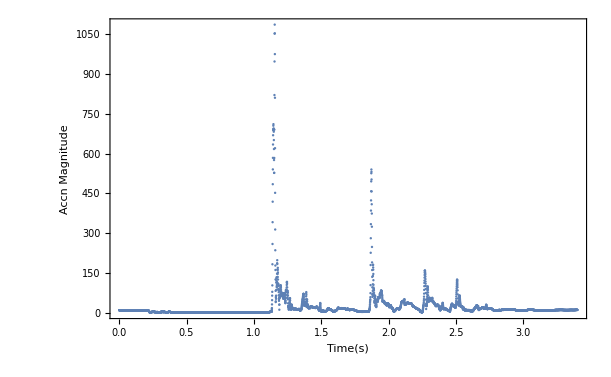

```mathematica
ListPlot[Table[{δt*i,Norm[-Graphics-[[i]]]},{i,Range[n]}],PlotRange->All,Frame->True,FrameLabel->{"Time(s)","Accn Magnitude"}]
```

```mathematica
ClearAll[CalibrateW]; (*Function to correct bias from the gyroscope data using a linear fit*)
CalibrateW[tvec_,wvec_]:=Module[{data,sol,wc,datac,c1,c2,δw},
data=MapThread[List,{tvec[[(CalTstart-Tstart)*freq+1;;(CalTend-Tstart) *freq]],wvec[[(CalTstart-Tstart)*freq +1;;(CalTend-Tstart) *freq]]}];
sol=FindFit[data,(*c1 t+*) c2,{(*c1,*)c2},t];
Echo[sol];
w1[t_]:=Evaluate[ ((*c1 t+*)c2)/.sol];

δw=Table[w1[ti],{ti,tvec}];
wc=wvec-δw;
datac=MapThread[List,{tvec,wc}];
wc
]
```

```mathematica
Unprotect[-Graphics-];
-Graphics- = MapThread[List , {CalibrateW[time,-Graphics-[[;;,1]]], CalibrateW[time,-Graphics-[[;;,2]]], CalibrateW[time,-Graphics-[[;;,3]]]}]; (*Corrected gyroscope data*)
Protect[-Graphics-];
```

{c2$10536→-0.0112393}

{c2$10541→0.0230334}

{c2$10543→-0.000734565}

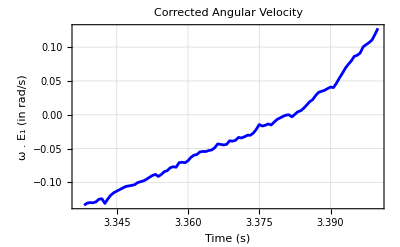

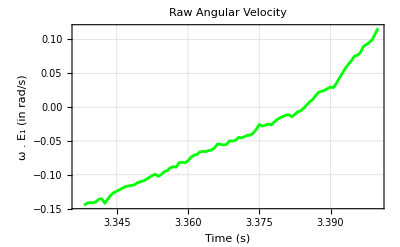

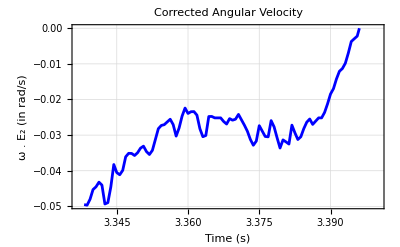

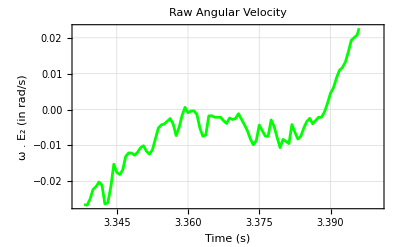

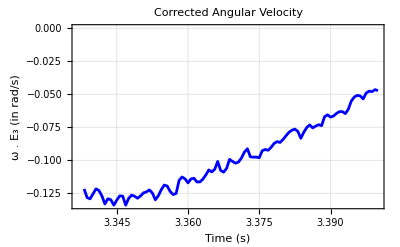

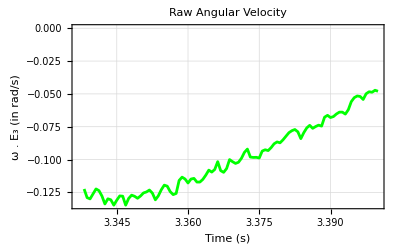

```mathematica
ListLinePlot[Transpose[{time[[-100;;-1]],-Graphics- [[-100;;-1,1]]}],Frame->True,PlotLabel->"Corrected Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_1 (in rad/s)",Bold,FontSize->13]},PlotStyle->Blue]
ListLinePlot[Transpose[{time[[-100;;-1]],-Graphics- [[-100;;-1,1]]}],Frame->True,PlotLabel->"Raw Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_1 (in rad/s)",Bold,FontSize->13]},PlotStyle->Green]
ListLinePlot[Transpose[{time[[-100;;-1]],-Graphics- [[-100;;-1,2]]}],Frame->True,PlotLabel->"Corrected Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_2 (in rad/s)",Bold,FontSize->13]},PlotStyle->Blue]
ListLinePlot[Transpose[{time[[-100;;-1]],-Graphics- [[-100;;-1,2]]}],Frame->True,PlotLabel->"Raw Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_2 (in rad/s)",Bold,FontSize->13]},PlotStyle->Green]
ListLinePlot[Transpose[{time[[-100;;-1]],-Graphics- [[-100;;-1,3]]}],Frame->True,PlotLabel->"Corrected Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_3 (in rad/s)",Bold,FontSize->13]},PlotStyle->Blue]
ListLinePlot[Transpose[{time[[-100;;-1]],-Graphics- [[-100;;-1,3]]}],Frame->True,PlotLabel->"Raw Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_3 (in rad/s)",Bold,FontSize->13]},PlotStyle->Green]
```

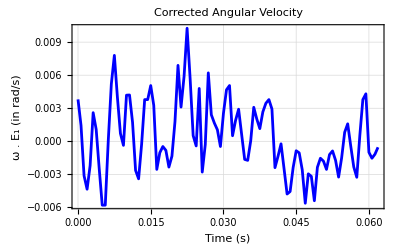

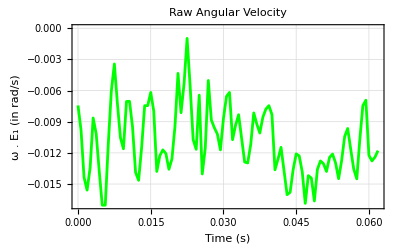

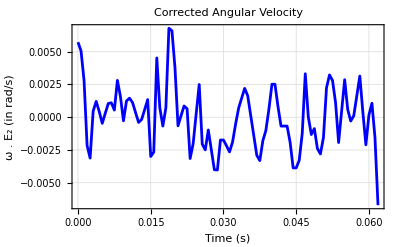

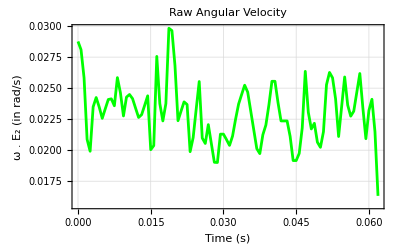

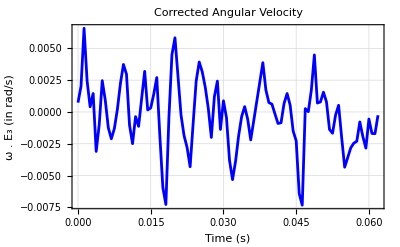

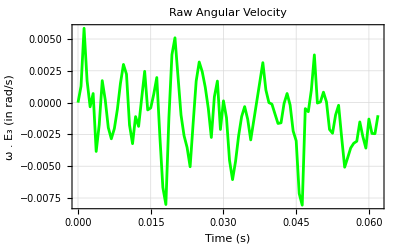

```mathematica
ListLinePlot[Transpose[{time[[1;;100]],-Graphics- [[1;;100,1]]}],Frame->True,PlotLabel->"Corrected Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_1 (in rad/s)",Bold,FontSize->13]},PlotStyle->Blue]
ListLinePlot[Transpose[{time[[1;;100]],-Graphics- [[1;;100,1]]}],Frame->True,PlotLabel->"Raw Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_1 (in rad/s)",Bold,FontSize->13]},PlotStyle->Green]
ListLinePlot[Transpose[{time[[1;;100]],-Graphics- [[1;;100,2]]}],Frame->True,PlotLabel->"Corrected Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_2 (in rad/s)",Bold,FontSize->13]},PlotStyle->Blue]
ListLinePlot[Transpose[{time[[1;;100]],-Graphics- [[1;;100,2]]}],Frame->True,PlotLabel->"Raw Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_2 (in rad/s)",Bold,FontSize->13]},PlotStyle->Green]
ListLinePlot[Transpose[{time[[1;;100]],-Graphics- [[1;;100,3]]}],Frame->True,PlotLabel->"Corrected Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_3 (in rad/s)",Bold,FontSize->13]},PlotStyle->Blue]
ListLinePlot[Transpose[{time[[1;;100]],-Graphics- [[1;;100,3]]}],Frame->True,PlotLabel->"Raw Angular Velocity",LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["ω . E_3 (in rad/s)",Bold,FontSize->13]},PlotStyle->Green]
```

### Algorithm

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Jeetika/Brown Dropbox/Jeetika Patangia/A1G1

#### Initial Conditions

```mathematica
-Graphics- = Id; (*Initial Rotation tensor at time t = 0*)
-Graphics- = {0,0,0};
-Graphics- ={0,0,0};
-Graphics- = {0,0,0};
γ = 1/2;    (*Newmark Beta Parameter*)
β = 1/4;  (*Newmark Beta Parameter*)
```

#### Step - 1 - Calculation of^1 A pseudo

```mathematica
-Graphics-[τ_]:=-Graphics-[[τ]][[1]] (-Graphics-)+-Graphics-[[τ]][[2]] (-Graphics-)+-Graphics-[[τ]][[3]] (-Graphics-);
```

#### Step -2 - Calculation of Angular Velocity Wbar and WbarPrime

```mathematica
Tilde[v_]:={{0,-v[[3]],v[[2]]},{v[[3]],0,-v[[1]]},{-v[[2]],v[[1]],0}};
```

```mathematica
wbar = Table[-Graphics-[[i,1]] -Graphics-+-Graphics-[[i,2]] -Graphics-+-Graphics-[[i,3]] -Graphics-,{i,Range[n]}];
```

```mathematica
-Graphics- = Table[Tilde[wbar[[i]]],{i,Range[n]}];
```

```mathematica
(*(*Five Point Scheme*)
wbarprime= {};
AppendTo[wbarprime,(wbar[[2]]-wbar[[1]])/δt];
AppendTo[wbarprime,(wbar[[3]]-wbar[[1]])/(2 δt)];
Do[
AppendTo[wbarprime,(- wbar[[i+2]] + 8 wbar[[i+1]] - 8 wbar[[i-1]] + wbar[[i-2]])/(12 δt)],
{i,3,n-2}]
AppendTo[wbarprime,(-wbar[[n-2]]+wbar[[n]])/(2 δt)];
AppendTo[wbarprime, (-wbar[[n-1]]+wbar[[n]])/δt];*)
```

```mathematica
(*Three Point Scheme*)
wbarprime= {};
AppendTo[wbarprime,(wbar[[2]]-wbar[[1]])/δt];
Do[
AppendTo[wbarprime,(wbar[[i+1]] -  wbar[[i-1]])/(2 δt)],
{i,2,n-1}]
AppendTo[wbarprime,(-wbar[[n-1]]+wbar[[n]])/δt];
```

```mathematica
-Graphics- = Table[Tilde[wbarprime[[i]]],{i,Range[n]}];
```

#### Step - 3 - Calculation of P matrix and q

```mathematica
-Graphics- = Table[-Graphics-[[i]].-Graphics-[[i]]+-Graphics-[[i]],{i,Range[n]}];
```

```mathematica
q = Table[-Graphics-[i]--Graphics-[[i]].-Graphics- ,{i,Range[n]}];
```

#### Step - 4 - Calculation of Q matrix

```mathematica
Hd[i_]:=Module[{term1,term},
term1 = If[i==n,δt -Graphics-[[i]],δt (-Graphics-[[i]]+ -Graphics-[[i-1]])/2];
term =-Normal@HodgeDual[term1];
Id + (Sinc[Norm[term]]term1) +1/2(Sinc[Norm[term]/2])^2 (term1.term1)
]
```

```mathematica
For[-Graphics-  ={};i=1,
i<=n,i++,
AppendTo[-Graphics- , If[i==1,-Graphics-,-Graphics-[[i-1]].Hd[i]]]
]
```

#### Calculation of c’’(τ) and then c(τ)

```mathematica
grav =Mean[Table[{-Graphics-[[i]].-Graphics-[i]},{i,1,0.1*1600}]][[1]];
```

```mathematica
-Graphics- = Table[-Graphics-[[i]].q[[i]]-grav,{i,1,n}];
```

```mathematica
For[-Graphics-= {};i=1,i<= n,i++,AppendTo[-Graphics-,If[i==1, -Graphics-,-Graphics-[[i-1]]+ δt((1 - γ)-Graphics-[[i-1]]+ γ-Graphics-[[i]])]]]
```

```mathematica
For[-Graphics-= {};i=1,i <= n, i++,AppendTo[-Graphics-, If[i ==1,-Graphics-,-Graphics-[[i-1]]+ δt -Graphics-[[i-1]] + δt*δt/2((1-2 β)-Graphics-[[i-1]]+ 2 β -Graphics-[[i]])]]]
```

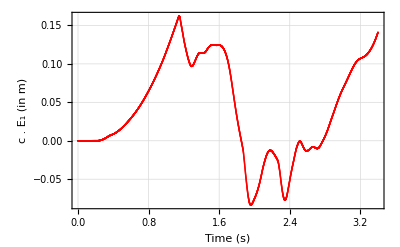

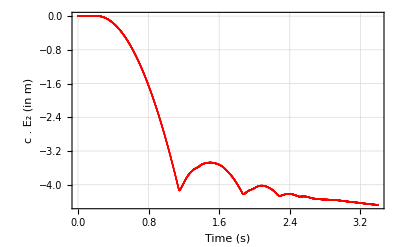

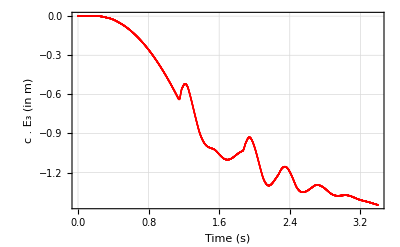

```mathematica
(*Plots of the translation like term c(τ)*)c1 = ListPlot[Table[{time[[i]],-Graphics-[[i,1]]},{i,Range[n]}],Frame->True,LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["c . E_1 (in m)",Bold,FontSize->13]},PlotStyle->Red]
c2 = ListPlot[Table[{time[[i]],-Graphics-[[i,2]]},{i,Range[n]}],Frame->True,LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["c . E_2 (in m)",Bold,FontSize->13]},PlotStyle->Red]
c3 = ListPlot[Table[{time[[i]],-Graphics-[[i,3]]},{i,Range[n]}],Frame->True,LabelStyle->Directive[Black,14],GridLines->Automatic,FrameLabel->{Style["Time (s)",Bold, FontSize->13],Style["c . E_3 (in m)",Bold,FontSize->13]},PlotStyle->Red]
```

```mathematica
Export["Translation_Plots/c_S1_Wbar_Avg_g.csv",-Graphics-];
```

```mathematica
ExpandFileName["Translation_Plots/c_S1_Wbar_Avg_g.csv"]
```

/Users/Jeetika/Brown Dropbox/Jeetika Patangia/A1G1/Translation_Plots/c_S1_Wbar_Avg_g.csv

```mathematica
Export["Translations/c1_S1_Wbar_Avg_g.png",c1];
Export["Translations/c2_S1_Wbar_Avg_g.png",c2];
Export["Translations/c3_S1_Wbar_Avg_g.png",c3];
```

## Motion recreation

```mathematica
ΒCon=Import["Rigid Cap Small 10 may.STL","PolygonData"];
ΒVer=Import["Rigid Cap Small 10 may.STL","VertexData"];
inchtometer=0.0254;
mmtometer=0.001;
(*centerpoint={23.5609,20.6667,11.7306}*inchtometer;*)
Subscript[Q, v]=RotationMatrix[(0/180)*π,{1,0,0}];
centerpoint={0,0,0}*mmtometer;
Subscript[φ, t0]=Map[AffineTransform[{IdentityMatrix[3],-centerpoint}],ΒVer*mmtometer] ;
Subscript[φ, t]=Map[AffineTransform[{-Graphics-[[#]].Subscript[Q, v],-Graphics-[[#]]}],Subscript[φ, t0]]& ;
```

```mathematica
MeshRegion[ΒVer*mmtometer,{
Triangle[ΒCon]},BaseStyle->{Gray,Specularity[5.0],Opacity[1]},Boxed->True,Axes->True,ViewPoint->{0,0,4},ViewVertical->{0,1,0},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
ImpactingHeadformAnimation =Table[MeshRegion[Subscript[φ, t][it],
{Triangle[ΒCon]},BaseStyle->{Gray,Specularity[5.0],Opacity[1]},
PlotRange->{{-0.5,0.5},{-5,0.3},{-1.3,2}},ImageSize->100,Boxed->False,Axes->False,ViewPoint->{0,0,3},ViewVertical->{0,1,0},Background->None
],{it,1,n,25}];
```

```mathematica
Do[Export[StringJoin["A1G1(V1)/frame_",StringPadLeft[ToString[i],4,"0"],".png"],ImpactingHeadformAnimation[[i]]],{i,Length[ImpactingHeadformAnimation]}]
```

```mathematica
ImpactingHeadformAnimation[[1]]
```

-Graphics3D-